```mathematica
SetDirectory["/home/atim/WORK/PULSARS/TDC/src/MATHEMATICA"];
```

```mathematica
σ[D_,K_,ϵ_,x_]:=x D Exp[- K/(ϵ x)];
```

```mathematica
τ[D_,K_,ϵ_,x_]:=Integrate[σ[D,K,ϵ,y],y]/.{y->x}
```

```mathematica
dndx[ϵ_,x_]:=Module[{D=2.248 10^6,K=7.486 10^5},Evaluate[Exp[-τ[d,k,ϵ,x]] σ[d,k,ϵ,x]]/.{d->D,k->K} ]
```

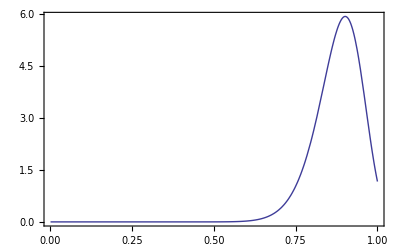

```mathematica
Plot[Evaluate[dndx[7 10^4,x]],{x,0.001,1}, PlotRange->All,Frame-> True]
```

```mathematica
dndxTable[ϵ_,L_,Ntot_:500]:=Table[{x,Max[Evaluate[dndx[ϵ,x]],10^-10]},{x,L/Ntot,L,L/Ntot}]
```

```mathematica
dndxTSave=dndxTable[7 10^4,1];
```

```mathematica
dndxTSave
```

{{1/500,1/10000000000},{1/250,1/10000000000},{3/500,1/10000000000},{1/125,1/10000000000},{1/100,1/10000000000},{3/250,1/10000000000},{7/500,1/10000000000},{2/125,1/10000000000},{9/500,1/10000000000},{1/50,1/10000000000},{11/500,1/10000000000},{3/125,1/10000000000},{13/500,1/10000000000},{7/250,1/10000000000},{3/100,1/10000000000},{4/125,1/10000000000},{17/500,1/10000000000},{9/250,1/10000000000},{19/500,1/10000000000},{1/25,1/10000000000},{21/500,1/10000000000},{11/250,1/10000000000},{23/500,1/10000000000},{6/125,1/10000000000},{1/20,1/10000000000},{13/250,1/10000000000},{27/500,1/10000000000},{7/125,1/10000000000},{29/500,1/10000000000},{3/50,1/10000000000},{31/500,1/10000000000},{8/125,1/10000000000},{33/500,1/10000000000},{17/250,1/10000000000},{7/100,1/10000000000},{9/125,1/10000000000},{37/500,1/10000000000},{19/250,1/10000000000},{39/500,1/10000000000},{2/25,1/10000000000},{41/500,1/10000000000},{21/250,1/10000000000},{43/500,1/10000000000},{11/125,1/10000000000},{9/100,1/10000000000},{23/250,1/10000000000},{47/500,1/10000000000},{12/125,1/10000000000},{49/500,1/10000000000},{1/10,1/10000000000},{51/500,1/10000000000},{13/125,1/10000000000},{53/500,1/10000000000},{27/250,1/10000000000},{11/100,1/10000000000},{14/125,1/10000000000},{57/500,1/10000000000},{29/250,1/10000000000},{59/500,1/10000000000},{3/25,1/10000000000},{61/500,1/10000000000},{31/250,1/10000000000},{63/500,1/10000000000},{16/125,1/10000000000},{13/100,1/10000000000},{33/250,1/10000000000},{67/500,1/10000000000},{17/125,1/10000000000},{69/500,1/10000000000},{7/50,1/10000000000},{71/500,1/10000000000},{18/125,1/10000000000},{73/500,1/10000000000},{37/250,1/10000000000},{3/20,1/10000000000},{19/125,1/10000000000},{77/500,1/10000000000},{39/250,1/10000000000},{79/500,1/10000000000},{4/25,1/10000000000},{81/500,1/10000000000},{41/250,1/10000000000},{83/500,1/10000000000},{21/125,1/10000000000},{17/100,1/10000000000},{43/250,1/10000000000},{87/500,1/10000000000},{22/125,1/10000000000},{89/500,1/10000000000},{9/50,1/10000000000},{91/500,1/10000000000},{23/125,1/10000000000},{93/500,1/10000000000},{47/250,1/10000000000},{19/100,1/10000000000},{24/125,1/10000000000},{97/500,1/10000000000},{49/250,1/10000000000},{99/500,1/10000000000},{1/5,1/10000000000},{101/500,1/10000000000},{51/250,1/10000000000},{103/500,1/10000000000},{26/125,1/10000000000},{21/100,1/10000000000},{53/250,1/10000000000},{107/500,1/10000000000},{27/125,1/10000000000},{109/500,1/10000000000},{11/50,1/10000000000},{111/500,1/10000000000},{28/125,1/10000000000},{113/500,1/10000000000},{57/250,1/10000000000},{23/100,1/10000000000},{29/125,1/10000000000},{117/500,1/10000000000},{59/250,1/10000000000},{119/500,1/10000000000},{6/25,1/10000000000},{121/500,1/10000000000},{61/250,1/10000000000},{123/500,1/10000000000},{31/125,1/10000000000},{1/4,1/10000000000},{63/250,1/10000000000},{127/500,1/10000000000},{32/125,1/10000000000},{129/500,1/10000000000},{13/50,1/10000000000},{131/500,1/10000000000},{33/125,1/10000000000},{133/500,1/10000000000},{67/250,1/10000000000},{27/100,1/10000000000},{34/125,1/10000000000},{137/500,1/10000000000},{69/250,1/10000000000},{139/500,1/10000000000},{7/25,1/10000000000},{141/500,1/10000000000},{71/250,1/10000000000},{143/500,1/10000000000},{36/125,1/10000000000},{29/100,1/10000000000},{73/250,1/10000000000},{147/500,1.25599×10^-10},{37/125,1.61494×10^-10},{149/500,2.06958×10^-10},{3/10,2.64357×10^-10},{151/500,3.36596×10^-10},{38/125,4.27236×10^-10},{153/500,5.40618×10^-10},{77/250,6.82031×10^-10},{31/100,8.57895×10^-10},{39/125,1.07598×10^-9},{157/500,1.34567×10^-9},{79/250,1.67827×10^-9},{159/500,2.08736×10^-9},{8/25,2.58919×10^-9},{161/500,3.2032×10^-9},{81/250,3.95259×10^-9},{163/500,4.86491×10^-9},{41/125,5.97288×10^-9},{33/100,7.31525×10^-9},{83/250,8.93778×10^-9},{167/500,1.08944×10^-8},{42/125,1.32486×10^-8},{169/500,1.60748×10^-8},{17/50,1.94603×10^-8},{171/500,2.3507×10^-8},{43/125,2.83338×10^-8},{173/500,3.40792×10^-8},{87/250,4.09041×10^-8},{7/20,4.89951×10^-8},{44/125,5.85683×10^-8},{177/500,6.98731×10^-8},{89/250,8.31974×10^-8},{179/500,9.88727×10^-8},{9/25,1.1728×10^-7},{181/500,1.38856×10^-7},{91/250,1.64102×10^-7},{183/500,1.9359×10^-7},{46/125,2.27973×10^-7},{37/100,2.67997×10^-7},{93/250,3.14509×10^-7},{187/500,3.68474×10^-7},{47/125,4.30983×10^-7},{189/500,5.03276×10^-7},{19/50,5.86753×10^-7},{191/500,6.82996×10^-7},{48/125,7.93791×10^-7},{193/500,9.21147×10^-7},{97/250,1.06733×10^-6},{39/100,1.23487×10^-6},{49/125,1.42663×10^-6},{197/500,1.64579×10^-6},{99/250,1.89593×10^-6},{199/500,2.18104×10^-6},{2/5,2.50557×10^-6},{201/500,2.8745×10^-6},{101/250,3.29335×10^-6},{203/500,3.76827×10^-6},{51/125,4.30608×10^-6},{41/100,4.91438×10^-6},{103/250,5.60154×10^-6},{207/500,6.37687×10^-6},{52/125,7.25064×10^-6},{209/500,8.2342×10^-6},{21/50,9.34008×10^-6},{211/500,0.0000105821},{53/125,0.0000119754},{213/500,0.0000135367},{107/250,0.0000152844},{43/100,0.0000172386},{54/125,0.0000194214},{217/500,0.0000218571},{109/250,0.0000245722},{219/500,0.0000275955},{11/25,0.0000309588},{221/500,0.0000346966},{111/250,0.0000388466},{223/500,0.0000434498},{56/125,0.0000485508},{9/20,0.0000541983},{113/250,0.000060445},{227/500,0.0000673482},{57/125,0.00007497},{229/500,0.000083378},{23/50,0.000092645},{231/500,0.00010285},{58/125,0.000114078},{233/500,0.000126423},{117/250,0.000139982},{47/100,0.000154864},{59/125,0.000171185},{237/500,0.00018907},{119/250,0.000208652},{239/500,0.000230076},{12/25,0.000253499},{241/500,0.000279086},{121/250,0.000307016},{243/500,0.000337483},{61/125,0.000370692},{49/100,0.000406863},{123/250,0.000446233},{247/500,0.000489056},{62/125,0.0005356},{249/500,0.000586155},{1/2,0.00064103},{251/500,0.000700554},{63/125,0.000765077},{253/500,0.000834974},{127/250,0.000910644},{51/100,0.000992511},{64/125,0.00108103},{257/500,0.00117667},{129/250,0.00127996},{259/500,0.00139143},{13/25,0.00151165},{261/500,0.00164125},{131/250,0.00178086},{263/500,0.00193118},{66/125,0.00209293},{53/100,0.00226688},{133/250,0.00245385},{267/500,0.0026547},{67/125,0.00287034},{269/500,0.00310174},{27/50,0.00334992},{271/500,0.00361594},{68/125,0.00390095},{273/500,0.00420614},{137/250,0.00453277},{11/20,0.00488217},{69/125,0.00525573},{277/500,0.00565494},{139/250,0.00608135},{279/500,0.00653657},{14/25,0.00702233},{281/500,0.00754044},{141/250,0.00809277},{283/500,0.00868132},{71/125,0.00930817},{57/100,0.00997552},{143/250,0.0106856},{287/500,0.011441},{72/125,0.012244},{289/500,0.0130974},{29/50,0.0140038},{291/500,0.0149663},{73/125,0.0159878},{293/500,0.0170715},{147/250,0.0182207},{59/100,0.0194388},{74/125,0.0207295},{297/500,0.0220965},{149/250,0.0235438},{299/500,0.0250754},{3/5,0.0266956},{301/500,0.0284088},{151/250,0.0302198},{303/500,0.0321334},{76/125,0.0341546},{61/100,0.0362885},{153/250,0.0385408},{307/500,0.040917},{77/125,0.0434231},{309/500,0.0460652},{31/50,0.0488496},{311/500,0.051783},{78/125,0.0548723},{313/500,0.0581245},{157/250,0.061547},{63/100,0.0651475},{79/125,0.068934},{317/500,0.0729147},{159/250,0.0770981},{319/500,0.081493},{16/25,0.0861086},{321/500,0.0909542},{161/250,0.0960398},{323/500,0.101375},{81/125,0.106971},{13/20,0.112839},{163/250,0.118988},{327/500,0.125431},{82/125,0.132181},{329/500,0.139247},{33/50,0.146645},{331/500,0.154386},{83/125,0.162484},{333/500,0.170952},{167/250,0.179805},{67/100,0.189057},{84/125,0.198724},{337/500,0.20882},{169/250,0.219362},{339/500,0.230365},{17/25,0.241847},{341/500,0.253824},{171/250,0.266313},{343/500,0.279333},{86/125,0.292902},{69/100,0.307038},{173/250,0.321761},{347/500,0.33709},{87/125,0.353045},{349/500,0.369647},{7/10,0.386916},{351/500,0.404872},{88/125,0.423539},{353/500,0.442937},{177/250,0.463088},{71/100,0.484016},{89/125,0.505742},{357/500,0.528291},{179/250,0.551685},{359/500,0.575948},{18/25,0.601104},{361/500,0.627176},{181/250,0.65419},{363/500,0.682169},{91/125,0.711138},{73/100,0.741122},{183/250,0.772144},{367/500,0.80423},{92/125,0.837404},{369/500,0.87169},{37/50,0.907112},{371/500,0.943694},{93/125,0.981459},{373/500,1.02043},{187/250,1.06063},{3/4,1.10209},{94/125,1.14481},{377/500,1.18884},{189/250,1.23417},{379/500,1.28084},{19/25,1.32886},{381/500,1.37825},{191/250,1.42903},{383/500,1.48121},{96/125,1.5348},{77/100,1.58981},{193/250,1.64626},{387/500,1.70416},{97/125,1.7635},{389/500,1.8243},{39/50,1.88656},{391/500,1.95027},{98/125,2.01544},{393/500,2.08206},{197/250,2.15012},{79/100,2.2196},{99/125,2.2905},{397/500,2.3628},{199/250,2.43647},{399/500,2.5115},{4/5,2.58784},{401/500,2.66547},{201/250,2.74436},{403/500,2.82445},{101/125,2.9057},{81/100,2.98807},{203/250,3.07149},{407/500,3.1559},{102/125,3.24124},{409/500,3.32744},{41/50,3.41441},{411/500,3.50208},{103/125,3.59036},{413/500,3.67914},{207/250,3.76833},{83/100,3.85783},{104/125,3.94751},{417/500,4.03727},{209/250,4.12696},{419/500,4.21647},{21/25,4.30566},{421/500,4.39437},{211/250,4.48246},{423/500,4.56978},{106/125,4.65616},{17/20,4.74143},{213/250,4.82542},{427/500,4.90796},{107/125,4.98886},{429/500,5.06794},{43/50,5.14501},{431/500,5.21986},{108/125,5.29231},{433/500,5.36215},{217/250,5.42919},{87/100,5.49322},{109/125,5.55403},{437/500,5.61143},{219/250,5.66521},{439/500,5.71517},{22/25,5.76111},{441/500,5.80284},{221/250,5.84017},{443/500,5.87291},{111/125,5.90089},{89/100,5.92393},{223/250,5.94187},{447/500,5.95456},{112/125,5.96185},{449/500,5.96362},{9/10,5.95974},{451/500,5.95011},{113/125,5.93465},{453/500,5.91327},{227/250,5.88591},{91/100,5.85255},{114/125,5.81315},{457/500,5.76771},{229/250,5.71626},{459/500,5.65883},{23/25,5.59548},{461/500,5.52629},{231/250,5.45136},{463/500,5.37082},{116/125,5.28481},{93/100,5.19351},{233/250,5.0971},{467/500,4.9958},{117/125,4.88983},{469/500,4.77946},{47/50,4.66494},{471/500,4.54657},{118/125,4.42466},{473/500,4.29953},{237/250,4.17152},{19/20,4.04097},{119/125,3.90824},{477/500,3.77371},{239/250,3.63774},{479/500,3.50071},{24/25,3.36302},{481/500,3.22504},{241/250,3.08715},{483/500,2.94973},{121/125,2.81315},{97/100,2.67777},{243/250,2.54395},{487/500,2.41202},{122/125,2.2823},{489/500,2.15511},{49/50,2.03073},{491/500,1.90942},{123/125,1.79144},{493/500,1.67701},{247/250,1.56633},{99/100,1.45956},{124/125,1.35687},{497/500,1.25838},{249/250,1.16418},{499/500,1.07435},{1,0.988933}}

```mathematica
Export["../../RESULTS/test_absorption/dndxT.h5",dndxTSave]
```

../../RESULTS/test_absorption/dndxT.h5